```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
<<Data`;
```

```mathematica
freq=Freq[];
data=nxrData[3];
```

```mathematica
(*Dimensions[dd[[2,1]]]
dd[[2,1]]*)
data//MatrixForm
d1=data[[1,1]];
```

(((3702.93
937.674) | (3428.75
1213.51) | (3210.87
1408.81) | (2988.39
1604.38) | (2877.74
1632.13) | (2825.45
1541.12) | (2776.
1481.) | (2729.86
1438.68) | (2690.58
1366.78) | (2629.73
1303.12) | (2614.92
1257.91) | (2588.65
1224.2) | (2554.13
1174.23) | (2531.41
1152.56) | (2510.13
1119.16) | (2471.95
1074.84) | (2455.67
1061.14) | (2444.97
1030.28) | (2422.35
1001.39) | (2420.6
989.8) | (2363.43
923.838) | (2386.92
922.952) | (2372.04
897.265)
(3306.61
960.034) | (3117.75
1170.64) | (2919.16
1390.49) | (2781.09
1468.78) | (2715.5
1423.86) | (2675.23
1358.99) | (2644.35
1308.64) | (2608.52
1265.5) | (2587.02
1222.88) | (2540.74
1169.15) | (2523.48
1148.95) | (2508.71
1104.38) | (2485.51
1085.89) | (2487.65
997.508) | (2428.18
1012.24) | (2413.29
972.095) | (2402.71
948.876) | (2389.54
930.68) | (2378.98
892.777) | (2354.84
876.226) | (2337.22
858.078) | (2326.37
826.096) | (2336.45
840.712)
(3591.93
1064.66) | (3356.47
1312.68) | (3225.43
1542.6) | (3063.23
1611.64) | (2986.34
1555.25) | (2957.55
1458.5) | (2924.5
1433.33) | (2891.73
1389.21) | (2834.86
1324.93) | (2793.87
1269.12) | (2786.56
1243.57) | (2757.06
1193.09) | (2723.19
1158.17) | (2712.98
1139.32) | (2696.79
1092.86) | (2676.18
1062.28) | (2676.29
1048.83) | (2661.11
1023.64) | (2665.63
1002.48) | (2643.13
968.817) | (2621.
966.937) | (2600.04
934.023) | (2624.69
940.809)
(1921.21
778.561) | (1898.85
733.469) | (1891.61
676.177) | (1867.64
656.236) | (1846.39
637.205) | (1832.32
602.792) | (1817.57
575.87) | (1804.26
552.994) | (1790.3
528.612) | (1787.35
508.13) | (1780.52
495.121) | (1766.42
472.981) | (1757.14
458.683) | (1741.35
447.75) | (1741.44
428.384) | (1734.6
418.682) | (1723.29
402.609) | (1719.29
391.875) | (1708.22
385.905) | (1715.19
390.626) | (1702.37
364.956) | (1692.73
360.42) | (1683.02
349.148)
(2415.26
1005.37) | (2379.1
1032.49) | (2341.3
962.625) | (2315.4
921.409) | (2287.97
879.644) | (2266.45
847.39) | (2252.44
813.148) | (2219.54
785.544) | (2218.71
753.152) | (2213.5
727.335) | (2202.52
718.194) | (2184.85
682.178) | (2163.8
663.192) | (2157.4
644.788) | (2141.63
626.662) | (2145.64
609.987) | (2133.14
591.171) | (2123.97
579.46) | (2105.64
555.94) | (2069.94
535.709) | (2069.86
530.294) | (2070.93
520.951) | (2071.07
520.218)
(2442.42
965.049) | (2351.57
1054.87) | (2330.79
998.014) | (2303.78
948.139) | (2275.05
905.811) | (2251.12
878.579) | (2234.88
844.49) | (2202.75
814.823) | (2211.02
787.308) | (2196.36
757.556) | (2184.56
736.883) | (2173.84
718.509) | (2158.44
689.677) | (2141.65
659.265) | (2136.25
655.157) | (2141.92
640.977) | (2132.23
620.68) | (2123.4
611.283) | (2121.24
579.112) | (2116.7
584.626) | (2110.55
589.674) | (2092.62
552.113) | (2069.7
548.385)) | ((2662.38
802.807) | (2522.13
965.125) | (2390.36
1180.87) | (2298.9
1177.42) | (2257.35
1120.56) | (2210.06
1089.88) | (2205.88
1042.71) | (2159.7
994.266) | (2162.5
968.692) | (2146.7
926.738) | (2113.88
894.244) | (2102.2
866.463) | (2078.06
835.796) | (2067.51
805.672) | (2051.51
791.199) | (2050.01
770.547) | (2040.43
744.673) | (2041.05
727.589) | (2028.93
709.726) | (2029.29
677.023) | (2005.28
676.019) | (2003.3
669.518) | (2002.
658.611)
(2693.46
847.696) | (2531.65
1057.97) | (2407.15
1224.39) | (2348.29
1173.37) | (2307.37
1114.44) | (2298.52
1057.69) | (2261.61
1040.23) | (2214.5
997.094) | (2225.9
965.079) | (2218.93
929.11) | (2188.73
907.051) | (2182.57
869.434) | (2160.59
848.903) | (2143.38
820.192) | (2142.57
794.261) | (2117.64
774.946) | (2109.56
761.985) | (2100.31
733.872) | (2094.48
715.468) | (2082.47
701.637) | (2071.46
681.062) | (2050.42
676.526) | (2050.48
667.824)
(3172.74
993.06) | (3011.21
1212.33) | (2834.8
1401.04) | (2755.9
1408.45) | (2722.86
1345.72) | (2687.35
1307.81) | (2670.27
1250.85) | (2625.26
1216.38) | (2602.29
1166.24) | (2587.88
1118.27) | (2572.38
1083.44) | (2560.5
1057.45) | (2536.38
1023.22) | (2510.36
987.337) | (2512.71
969.572) | (2504.02
935.716) | (2483.44
910.776) | (2484.79
894.088) | (2473.55
873.986) | (2467.25
844.728) | (2456.43
830.498) | (2446.59
816.719) | (2466.23
815.627)
(1816.67
737.674) | (1798.09
698.515) | (1789.72
652.465) | (1765.45
617.561) | (1754.39
595.534) | (1746.
565.625) | (1734.78
539.992) | (1728.86
520.985) | (1711.87
496.696) | (1710.49
475.327) | (1696.8
454.021) | (1693.47
440.485) | (1687.39
432.621) | (1679.39
416.229) | (1673.36
400.811) | (1669.54
389.436) | (1663.09
376.624) | (1656.33
366.592) | (1650.79
355.405) | (1658.86
369.28) | (1638.2
341.342) | (1633.79
334.775) | (1631.48
319.789)
(2309.82
950.624) | (2248.85
984.836) | (2230.03
918.241) | (2210.55
883.711) | (2180.05
843.399) | (2157.45
802.779) | (2136.31
767.854) | (2107.68
736.034) | (2114.52
710.793) | (2100.8
680.97) | (2089.32
655.955) | (2080.07
634.749) | (2065.86
612.328) | (2072.46
591.92) | (2041.73
579.291) | (2043.16
555.115) | (2029.72
537.032) | (2025.85
528.45) | (2015.71
519.048) | (2015.64
511.534) | (2007.41
484.903) | (1986.09
485.626) | (2018.93
477.998)
(2291.9
919.479) | (2218.83
986.961) | (2194.26
946.36) | (2160.63
898.939) | (2131.26
860.218) | (2132.73
821.671) | (2119.51
788.659) | (2092.18
759.01) | (2091.49
735.708) | (2085.78
710.058) | (2071.65
685.936) | (2059.07
661.889) | (2042.78
639.387) | (2042.25
636.48) | (2032.01
604.996) | (2030.74
586.143) | (2021.69
569.032) | (2013.41
550.428) | (2008.1
540.323) | (1990.38
519.196) | (1993.24
515.487) | (1987.32
509.147) | (1981.22
492.505))
((1881.64
756.796) | (1877.27
750.854) | (1841.7
639.545) | (1790.07
587.161) | (1783.02
553.643) | (1769.37
528.144) | (1750.12
488.643) | (1747.85
463.435) | (1740.98
441.829) | (1743.19
427.2) | (1730.7
410.396) | (1726.1
390.26) | (1719.61
373.678) | (1703.01
365.095) | (1710.64
346.791) | (1702.96
340.286) | (1698.51
327.082) | (1689.34
314.93) | (1684.78
320.78) | (1689.18
299.368) | (1686.49
296.766) | (1695.62
294.409) | (1702.31
279.069)
(1874.26
660.768) | (1840.29
600.079) | (1836.12
539.704) | (1812.2
508.705) | (1820.38
491.517) | (1794.76
461.817) | (1790.54
439.467) | (1789.82
412.884) | (1780.96
404.625) | (1776.72
389.988) | (1772.78
375.199) | (1759.81
356.438) | (1770.5
346.076) | (1753.04
333.776) | (1751.19
317.297) | (1735.58
302.906) | (1715.87
284.984) | (1719.73
282.234) | (1714.04
272.704) | (1699.63
269.498) | (1700.87
255.715) | (1703.21
249.079) | (1692.9
237.018)
(1958.02
780.378) | (1956.66
726.898) | (1932.03
684.925) | (1914.04
644.517) | (1890.79
603.793) | (1851.69
544.278) | (1852.3
518.216) | (1845.29
499.625) | (1830.2
466.173) | (1824.46
449.143) | (1824.97
428.044) | (1822.16
420.009) | (1806.93
394.635) | (1808.97
383.189) | (1792.81
364.752) | (1786.09
355.275) | (1775.73
340.023) | (1773.55
330.949) | (1770.83
322.133) | (1753.84
306.094) | (1751.67
299.419) | (1750.4
290.719) | (1742.24
279.062)
(1815.84
597.721) | (1804.86
555.248) | (1803.64
505.961) | (1781.66
477.729) | (1793.73
468.569) | (1763.88
440.767) | (1756.44
411.645) | (1756.32
391.94) | (1738.71
374.016) | (1733.41
355.503) | (1735.88
357.903) | (1729.62
347.182) | (1723.09
335.871) | (1728.3
345.349) | (1726.56
336.859) | (1725.41
327.891) | (1724.12
318.303) | (1717.7
299.786) | (1708.17
287.689) | (1705.44
281.416) | (1697.63
282.259) | (1688.65
267.153) | (1681.49
253.401)
(1948.84
725.928) | (1921.88
660.255) | (1920.59
632.202) | (1910.25
592.05) | (1900.95
567.06) | (1889.57
529.71) | (1889.5
508.41) | (1878.66
476.421) | (1872.93
459.69) | (1868.92
442.828) | (1860.03
420.199) | (1850.45
408.203) | (1847.3
391.645) | (1837.39
374.156) | (1832.38
359.167) | (1828.61
347.834) | (1825.31
333.361) | (1820.41
323.937) | (1824.51
307.284) | (1825.36
305.133) | (1814.4
294.844) | (1805.08
285.896) | (1794.25
270.715)
(1885.32
664.665) | (1874.68
610.928) | (1871.39
559.666) | (1853.35
542.308) | (1845.26
507.577) | (1839.41
483.932) | (1831.62
462.79) | (1829.53
445.654) | (1817.55
430.655) | (1816.91
407.125) | (1813.08
392.332) | (1801.76
376.408) | (1797.97
356.659) | (1792.3
344.17) | (1788.42
332.432) | (1772.41
329.137) | (1778.37
306.858) | (1772.44
298.195) | (1767.96
294.586) | (1754.95
269.486) | (1752.33
257.825) | (1752.18
264.367) | (1746.96
249.251)) | ((1666.52
613.821) | (1664.28
561.708) | (1652.08
527.883) | (1640.09
504.558) | (1638.44
481.908) | (1633.84
456.79) | (1624.88
435.69) | (1638.17
417.564) | (1611.43
396.7) | (1612.1
379.897) | (1604.28
359.481) | (1598.36
352.301) | (1596.95
341.773) | (1589.41
330.309) | (1597.
317.373) | (1585.94
310.287) | (1583.99
295.863) | (1584.75
289.712) | (1572.48
278.12) | (1565.48
280.546) | (1567.13
264.779) | (1567.04
254.928) | (1560.53
247.444)
(1707.12
569.868) | (1690.29
536.84) | (1699.05
484.309) | (1679.65
461.392) | (1675.64
447.421) | (1671.15
427.213) | (1666.49
405.321) | (1678.85
387.284) | (1655.09
370.564) | (1650.85
352.404) | (1643.61
336.787) | (1641.58
326.829) | (1635.08
310.725) | (1627.23
307.174) | (1633.38
289.478) | (1625.31
282.201) | (1617.67
274.77) | (1615.56
260.217) | (1613.55
257.872) | (1606.06
245.188) | (1601.53
243.066) | (1602.31
239.753) | (1598.46
222.373)
(1835.14
658.884) | (1844.4
603.199) | (1816.6
580.45) | (1811.4
540.347) | (1800.96
512.338) | (1792.18
498.026) | (1784.97
464.949) | (1787.07
436.964) | (1774.46
421.754) | (1771.66
398.936) | (1763.78
381.342) | (1756.2
367.53) | (1754.6
358.253) | (1749.15
345.072) | (1744.63
329.335) | (1739.05
326.083) | (1736.25
306.46) | (1727.18
298.956) | (1720.42
294.385) | (1723.16
282.796) | (1712.53
274.61) | (1713.53
270.783) | (1705.81
248.546)
(1793.51
634.761) | (1763.66
616.242) | (1771.59
543.32) | (1763.21
520.948) | (1759.46
498.21) | (1754.76
471.499) | (1749.11
449.419) | (1753.06
429.621) | (1735.84
409.376) | (1728.72
398.154) | (1729.91
379.395) | (1722.42
364.227) | (1717.98
350.463) | (1704.55
333.493) | (1711.
322.678) | (1699.66
316.854) | (1700.12
304.063) | (1696.74
300.096) | (1685.38
281.432) | (1690.51
282.288) | (1685.94
277.896) | (1679.03
266.533) | (1675.2
255.145)
(1961.
717.236) | (1951.78
670.146) | (1935.9
619.314) | (1931.76
576.985) | (1913.06
559.781) | (1917.18
535.288) | (1906.32
504.74) | (1893.64
478.814) | (1891.62
461.478) | (1885.88
434.002) | (1877.55
421.746) | (1865.75
402.026) | (1860.32
387.287) | (1853.96
373.151) | (1849.63
351.497) | (1843.48
349.33) | (1838.75
334.49) | (1832.33
334.313) | (1830.93
324.16) | (1825.68
300.276) | (1811.22
285.248) | (1814.24
271.14) | (1803.33
272.084)
(1907.37
643.755) | (1884.61
606.897) | (1882.53
563.355) | (1861.38
540.78) | (1857.41
512.662) | (1852.84
484.701) | (1856.56
471.16) | (1849.24
445.33) | (1834.14
417.718) | (1824.44
396.125) | (1816.48
383.786) | (1809.6
366.852) | (1799.99
348.253) | (1800.24
330.406) | (1791.16
320.021) | (1791.17
326.803) | (1785.47
301.028) | (1785.59
290.481) | (1779.57
272.948) | (1775.35
276.743) | (1768.75
275.397) | (1762.98
252.793) | (1761.48
238.475))
((2042.3
721.613) | (1878.87
877.329) | (1866.99
835.537) | (1847.97
793.952) | (1829.45
746.583) | (1824.31
718.248) | (1814.29
669.686) | (1801.17
639.952) | (1796.95
607.185) | (1790.3
577.216) | (1786.43
558.465) | (1774.87
535.865) | (1756.02
507.182) | (1754.77
476.432) | (1750.12
441.548) | (1748.2
444.636) | (1740.37
429.408) | (1730.27
403.284) | (1743.02
407.538) | (1751.1
387.248) | (1721.43
377.222) | (1720.33
361.277) | (1695.42
350.796)
(2146.15
845.823) | (2079.73
909.478) | (2079.7
856.767) | (2037.93
810.166) | (2038.77
765.917) | (2024.1
731.118) | (2012.65
680.852) | (1995.22
658.698) | (1997.7
627.19) | (1969.93
585.766) | (1947.14
544.384) | (1922.67
514.1) | (1918.95
504.143) | (1918.4
472.624) | (1906.48
457.353) | (1912.07
434.762) | (1895.04
413.879) | (1899.2
407.847) | (1907.04
366.548) | (1911.29
379.139) | (1895.9
369.213) | (1880.36
348.843) | (1885.86
318.631)
(2091.34
862.841) | (2035.5
888.441) | (2034.44
841.443) | (2016.49
786.602) | (1988.81
751.509) | (1971.54
710.966) | (1965.98
670.806) | (1952.1
639.929) | (1948.27
610.552) | (1948.45
576.048) | (1949.16
564.439) | (1941.91
539.999) | (1939.47
516.053) | (1932.43
500.84) | (1924.06
467.613) | (1919.3
455.827) | (1919.23
444.147) | (1921.79
434.856) | (1907.83
422.955) | (1896.1
403.719) | (1892.85
381.666) | (1892.88
373.085) | (1898.23
374.483)
(2043.6
831.9) | (2034.68
779.41) | (2022.87
737.463) | (2003.47
696.114) | (2005.13
656.153) | (1996.73
633.783) | (1988.92
589.523) | (1973.34
553.565) | (1973.8
535.901) | (1967.41
511.371) | (1972.56
483.412) | (1956.15
468.547) | (1950.42
449.572) | (1949.22
439.99) | (1935.48
406.459) | (1930.07
410.249) | (1923.4
392.019) | (1909.77
366.726) | (1921.11
365.081) | (1927.89
379.286) | (1921.85
344.065) | (1913.52
331.21) | (1907.55
333.263)
(2133.94
870.844) | (2085.18
835.7) | (2079.16
780.264) | (2061.3
738.053) | (2034.12
694.85) | (2028.17
656.254) | (2014.11
619.622) | (1997.16
593.103) | (2001.06
564.734) | (1998.44
530.625) | (1994.64
522.54) | (1989.24
500.769) | (1984.42
459.6) | (1968.36
456.24) | (1984.67
461.483) | (1967.77
422.572) | (1954.83
401.269) | (1957.46
400.385) | (1959.94
372.461) | (1957.66
372.381) | (1932.57
350.163) | (1950.48
352.353) | (1938.56
332.757)
(2169.67
909.374) | (2173.98
858.985) | (2151.73
825.541) | (2148.39
766.273) | (2131.88
720.359) | (2114.17
681.637) | (2108.31
653.034) | (2088.33
610.672) | (2094.79
583.694) | (2084.82
553.17) | (2080.81
537.746) | (2068.46
507.679) | (2074.49
482.367) | (2062.25
478.383) | (2052.19
438.827) | (2054.93
440.163) | (2047.78
418.86) | (2057.87
413.819) | (2053.88
381.776) | (2042.15
407.322) | (2030.75
361.001) | (2038.96
345.962) | (2032.51
341.219)) | ((1913.78
764.294) | (1852.45
818.186) | (1845.79
777.417) | (1829.13
717.196) | (1811.41
686.283) | (1820.24
665.394) | (1798.26
614.631) | (1783.7
592.322) | (1780.02
559.531) | (1775.23
536.311) | (1771.91
522.509) | (1761.77
494.217) | (1759.
473.297) | (1752.31
457.423) | (1760.62
447.14) | (1740.39
423.617) | (1728.89
403.917) | (1731.92
407.814) | (1724.31
376.906) | (1734.64
369.658) | (1721.62
356.218) | (1720.72
351.335) | (1729.61
334.011)
(2018.65
868.534) | (2013.52
818.015) | (2009.56
779.861) | (1967.25
722.639) | (1980.33
699.716) | (1977.69
663.646) | (1962.91
630.977) | (1958.13
600.904) | (1958.36
574.519) | (1961.02
551.219) | (1948.57
519.93) | (1946.76
498.755) | (1940.52
495.355) | (1931.16
471.838) | (1919.67
453.792) | (1924.88
438.382) | (1916.26
417.111) | (1898.59
421.603) | (1901.96
398.379) | (1919.04
377.197) | (1900.62
371.509) | (1900.98
357.819) | (1877.19
324.585)
(2141.47
839.231) | (2060.88
916.7) | (2057.18
859.273) | (2031.6
817.523) | (2012.22
763.165) | (2029.53
754.777) | (2004.14
701.055) | (1985.14
662.679) | (1985.65
638.288) | (1983.39
602.978) | (1973.68
584.256) | (1973.85
555.94) | (1958.6
554.598) | (1952.39
519.127) | (1918.7
506.942) | (1944.4
476.151) | (1933.6
461.362) | (1947.19
446.682) | (1933.53
432.549) | (1925.54
432.173) | (1914.46
394.027) | (1915.26
391.406) | (1903.82
390.106)
(2053.2
880.429) | (2030.73
812.233) | (2017.23
763.857) | (2011.68
710.793) | (1998.25
682.986) | (1978.74
670.151) | (1978.41
615.068) | (1965.11
586.198) | (1965.16
559.048) | (1962.7
532.519) | (1958.81
507.313) | (1943.97
490.816) | (1933.2
472.693) | (1937.8
451.297) | (1905.86
447.717) | (1919.58
421.695) | (1913.95
408.219) | (1903.22
393.445) | (1904.17
391.216) | (1893.79
377.042) | (1885.9
372.734) | (1878.31
352.874) | (1866.65
332.837)
(2159.53
830.265) | (2090.07
926.19) | (2084.93
884.572) | (2071.55
827.721) | (2052.67
775.229) | (2027.04
727.781) | (2028.47
703.609) | (1995.84
664.702) | (2004.4
635.063) | (2000.23
600.479) | (1993.18
578.317) | (1984.92
553.078) | (1971.8
529.448) | (1960.8
505.638) | (1966.52
496.51) | (1955.96
474.281) | (1952.53
460.84) | (1961.07
426.149) | (1940.7
425.271) | (1948.63
432.358) | (1938.53
393.341) | (1932.3
380.153) | (1923.5
364.839)
(2183.34
847.299) | (2149.46
944.443) | (2134.52
884.148) | (2113.05
830.648) | (2098.33
789.128) | (2092.75
747.666) | (2081.59
709.44) | (2058.26
673.538) | (2070.81
640.23) | (2067.26
613.135) | (2063.62
590.174) | (2056.13
564.422) | (2042.36
555.663) | (2045.8
529.46) | (2031.1
505.282) | (2037.08
473.294) | (2029.65
462.243) | (2025.98
455.459) | (2017.67
431.814) | (2013.
426.408) | (2007.33
410.221) | (2005.07
395.197) | (2008.69
397.368)))

{{3702.93,937.674},{3428.75,1213.51},{3210.87,1408.81},{2988.39,1604.38},{2877.74,1632.13},{2825.45,1541.12},{2776.,1481.},{2729.86,1438.68},{2690.58,1366.78},{2629.73,1303.12},{2614.92,1257.91},{2588.65,1224.2},{2554.13,1174.23},{2531.41,1152.56},{2510.13,1119.16},{2471.95,1074.84},{2455.67,1061.14},{2444.97,1030.28},{2422.35,1001.39},{2420.6,989.8},{2363.43,923.838},{2386.92,922.952},{2372.04,897.265}}

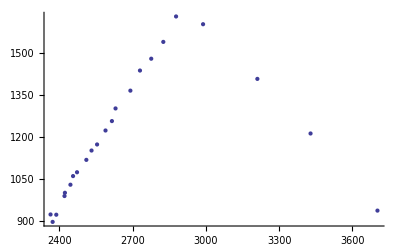

```mathematica
(*data=dd[[2,1]];*)
(*filter fitted data*)
(*For[i=1,i≤Length[data*)
(*data//MatrixForm;*)
(*dxy=Table[d1[[i]][[1]]Cos[d1[[i]][[2]] π/180]+ⅈ d1[[i]][[1]]Sin[d1[[i]][[2]] π/180],{i,Length[d1]}];*)
d11=d1[[1]]
ListPlot[d11]
```

{{13233.5+0. ⅈ,5048.52+0. ⅈ},{278.169-883.748 ⅈ,417.023+42.9789 ⅈ},{86.6475-441.702 ⅈ,381.45-96.9451 ⅈ},{79.81-254.918 ⅈ,286.348-154.439 ⅈ},{98.5007-177.554 ⅈ,212.741-160.9 ⅈ},{100.494-112.567 ⅈ,150.855-137.429 ⅈ},{107.815-79.6877 ⅈ,115.349-94.6952 ⅈ},{104.197-79.562 ⅈ,106.671-58.6431 ⅈ},{86.1458-48.8651 ⅈ,120.057-32.871 ⅈ},{92.1998-51.9774 ⅈ,125.926-22.8353 ⅈ},{104.355-33.3137 ⅈ,120.545-18.7818 ⅈ},{113.429-10.4157 ⅈ,127.501-1.6088 ⅈ},{113.429+10.4157 ⅈ,127.501+1.6088 ⅈ},{104.355+33.3137 ⅈ,120.545+18.7818 ⅈ},{92.1998+51.9774 ⅈ,125.926+22.8353 ⅈ},{86.1458+48.8651 ⅈ,120.057+32.871 ⅈ},{104.197+79.562 ⅈ,106.671+58.6431 ⅈ},{107.815+79.6877 ⅈ,115.349+94.6952 ⅈ},{100.494+112.567 ⅈ,150.855+137.429 ⅈ},{98.5007+177.554 ⅈ,212.741+160.9 ⅈ},{79.81+254.918 ⅈ,286.348+154.439 ⅈ},{86.6475+441.702 ⅈ,381.45+96.9451 ⅈ},{278.169+883.748 ⅈ,417.023-42.9789 ⅈ}}

23

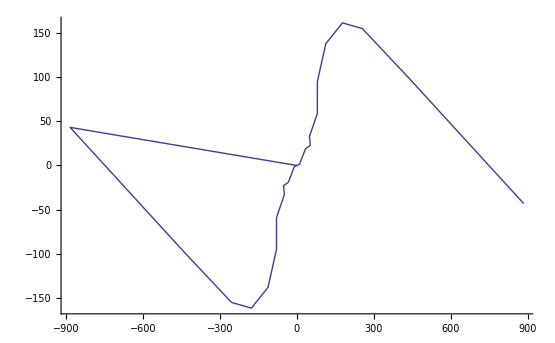

```mathematica
fdxy=InverseFourier[d11]
Length[fdxy]
ListPlot[Im[fdxy],Joined->True(*,PlotRange->{{0,33},{-60,100}}*)]
```

```mathematica
fdxy2=Delete[fdxy,{-1}]
```

{317.919-47.2974 ⅈ,4.92492-30.0209 ⅈ,-1.12244-15.4026 ⅈ,3.05734-6.73853 ⅈ,4.94916-6.35629 ⅈ,2.77159-5.32735 ⅈ,2.58197-3.69488 ⅈ,4.0996-3.12508 ⅈ,3.45267-2.99555 ⅈ,2.8244-2.33659 ⅈ,3.26897-1.6627 ⅈ,3.57917-1.63786 ⅈ,2.99634-1.31408 ⅈ,2.90963-0.779541 ⅈ,3.3625-0.565658 ⅈ,3.07188-0.392881 ⅈ,2.86366+0.145586 ⅈ,3.02265+0.406524 ⅈ,3.32022+0.560821 ⅈ,2.89638+1.03834 ⅈ,2.60962+1.36559 ⅈ,3.03048+1.74425 ⅈ,2.99308+2.03597 ⅈ,2.61202+2.77251 ⅈ,2.44399+3.60537 ⅈ,3.45334+3.79562 ⅈ,2.94717+4.68405 ⅈ,1.73604+6.89017 ⅈ,3.99919+9.10884 ⅈ,5.19833+8.35126 ⅈ,1.96988+17.8928 ⅈ}

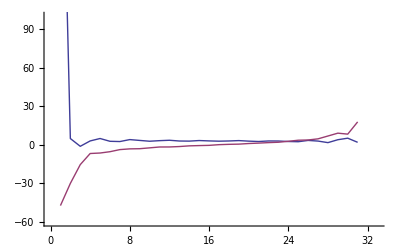

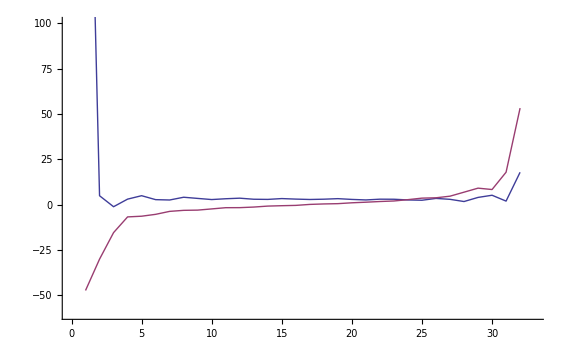

```mathematica
ListPlot[{Re[fdxy2],Im[fdxy2]},Joined->True,PlotRange->{{0,33},{-60,100}}]
```

(73.5919 | -11.7193
70.4914 | -10.8395
68.645 | -11.7138
67.3812 | -11.6887
66.3532 | -11.0089
65.5632 | -10.3277
64.6673 | -9.33618
64.0411 | -8.19861
63.6205 | -6.58715
63.5135 | -3.89955
61.6608 | -4.11037
60.4843 | -5.19946
59.2563 | -6.07396
58.2554 | -6.85456
57.2912 | -7.26074
56.4188 | -7.66349
55.5925 | -7.95784
54.823 | -8.13104
54.1228 | -7.78268
53.4663 | -7.9283
52.5747 | -8.19604
51.861 | -8.43106
51.1546 | -8.51211
50.3415 | -7.41639
49.6232 | -7.63185
48.5925 | -8.16832
47.648 | -8.73028
46.6456 | -9.43212
45.5252 | -10.0694
44.3443 | -10.8386
42.5465 | -11.633)

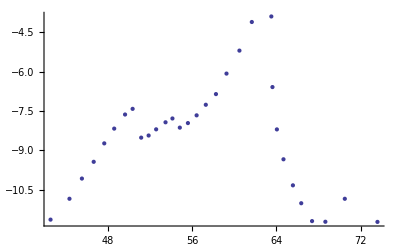

```mathematica
dxy2=Fourier[fdxy2];
Transpose[Join[{Re[dxy2]},{Im[dxy2]}]]//MatrixForm
ListPlot[Transpose[Join[{Re[dxy2]},{Im[dxy2]}]]]
```

```mathematica
(*d1=DeleteDuplicates[Flatten[Outer[EuclideanDistance,data[[1]],data[[1]],1]]];
d2=DeleteDuplicates[Flatten[Outer[EuclideanDistance,data[[1]],data[[2]],1]]];
ds=Reap[For[i=1,i≤31,i++,
For[j=1,j≤31,j++,
Sow[Flatten[Outer[EuclideanDistance,data[[i]],data[[j]],1]]]]]
]*)
```

```mathematica
<<BISfit`
```

```mathematica
data[[9]];
fd=Filterd[data[[9]]];
fdata=Map[Filterd,data];
fdata[[All,All,1]];
ListPlot[fdata[[All,All,2]]];
(*data[[5]]=Filterd[data[[5]]]*)
```

```mathematica
Dimensions[fdata[[1]]]
fdata//MatrixForm;
Min[fdata[[All,All,1]]]
```

{8,3}

80.0558

```mathematica
(*{mx1,mn1}={maxd,mind}/.{maxd->{200,120},mind->{65,10}}
td=fdata[[9]]
td[[2]]⟦1⟧>mx1[[1]]
For[i=1,i≤Length[td],i,
(*Another value boundary*)
If[td[[i]]⟦1⟧>mx1[[1]]||td[[i]][[2]]>mx1[[2]]||td[[i]]⟦1⟧<mn1[[1]]||td[[i]][[2]]<mn1[[2]],td=Drop[td,{i}];Continue[],i++];
];*)
d1=Table[StandardDeviation[Flatten[fdata[[All,All,i]]]],{i,3}]
Mdistance[u_,v_]:=√(∑ _(i=1)^Length[u] ((u[[i]]-v[[i]])/d1[[i]])^2);
```

{14.0281,9.99842,0.0917497}

```mathematica
(*ddsf[d_]:=Module[
{},

Dimensions[Flatten[ds[[2,1]],1]]*)

ddiff=Flatten[Reap[For[i=1,i≤3,i++,
For[j=i+1,j≤15,j++,
Sow[Flatten[Outer[EuclideanDistance,fdata[[i]],fdata[[j]],1]]]
]]
][[2,1]]];
dsame=Reap[For[i=1,i≤15,i++,
For[j=1,j≤Length[fdata[[i]]]-1,j++,
For[k=j+1,k<=Length[fdata[[i]]],k++,
Sow[EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];
(*Sow[-Mdistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]]]
][[2,1]];
```

```mathematica
mdsame=Mean[dsame]
mddiff=Mean[ddiff]
ddsame=StandardDeviation[dsame]
dddiff=StandardDeviation[ddiff]
Length[dsame]
Length[ddiff]
Max[ddiff]
Max[dsame]
```

5.43135

21.9346

5.87318

14.2251

307

1992

54.771

26.8119

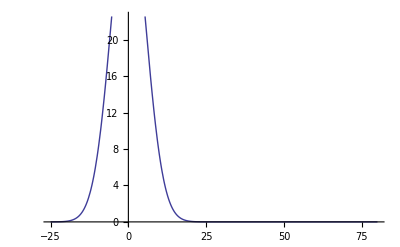

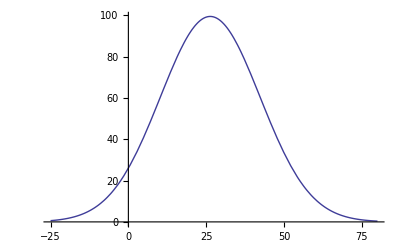

```mathematica
(*Ppdf1=Plot[500*PDF[NormalDistribution[mdsame,ddsame-7],x],{x,-25,80}]
Ppdf2=Plot[4000*PDF[NormalDistribution[mddiff,dddiff],x],{x,-25,80}]*)
```

```mathematica
sdsame=MovingAverage[dsame,{1,1,1}];
sddiff=MovingAverage[ddiff,{1,1,1}];
(*类概率密度*)
Pd=Length[ddiff]/(Length[dsame]+Length[ddiff]);
Ps=Length[dsame]/(Length[dsame]+Length[ddiff]);
```

```mathematica
h1=Histogram[Ps*sdsame,{0,10,0.1},ColorFunction->Function[{x},Black]]
(*BinCounts[Flatten[ds[[2,1]],1],1]*)
```

-Graphics-

```mathematica
(*Show[Ppdf1,h1,PlotRange->{{-5,25},{0,80}}]*)
```

-Graphics-

```mathematica
h2=Histogram[Pd*sddiff,{0,30,0.1}]
```

-Graphics-

```mathematica
(*Show[Ppdf2,h2,PlotRange->{{0,100},{0,100}}]*)
```

-Graphics-

```mathematica
Show[h2,h1,PlotRange->{{0,10},{0,80}}]
```

-Graphics-

307/2299

1992/2299

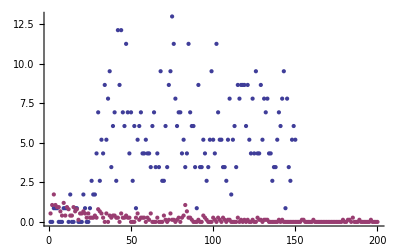

0.85

```mathematica
(*first *)
(*Pd=Length[ddiff]/(Length[dsame]+Length[ddiff]);
Ps=Length[dsame]/(Length[dsame]+Length[ddiff]);*)
(*find when his1=his2*)
bcdiff=Pd*BinCounts[ddiff,{0,15,0.1}];
bcsame=Ps*BinCounts[dsame,{0,20,0.1}];
Ps
Pd
ListPlot[{bcdiff,bcsame}]
l=Min[Length[bcdiff],Length[bcsame]];
dbc=bcsame[[1;;l]]-bcdiff[[1;;l]];
sdbc=MovingAverage[dbc,{1,1,1}];
t=1;k=1;
For[i=1,i≤l,i++,
If[sdbc[[i]]>0,t=i,
If[sdbc[[i]]<0,k=i;Break[],]
]
]
thd=(t+k)/2*0.1
```

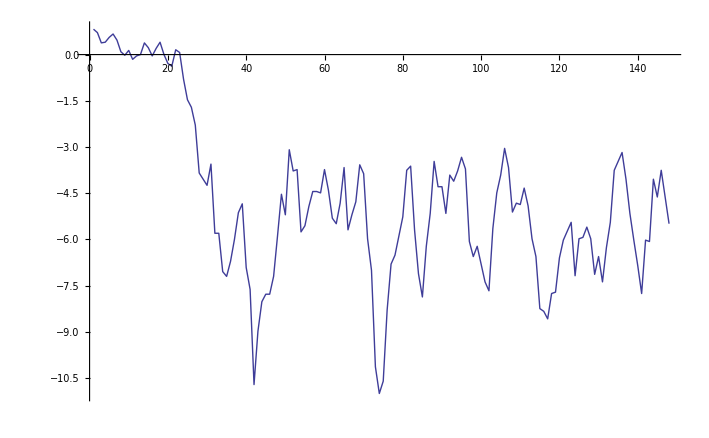

```mathematica
ListLinePlot[sdbc]
```

```mathematica
(*For[i=1,i≤Length[ddiff],i,
If[ddiff[i]>200000,ddiff=Delete[ddiff,i],i++]];*)
```

```mathematica
(*Position[ddiff,Select[ddiff,#>200000&]]
Length[tdd]*)
```

```mathematica
thd=9
ddiff2=Flatten[Reap[For[i=15,i≤30,i++,
For[j=i+1,j≤31,j++,
Sow[Flatten[Outer[EuclideanDistance,fdata[[i]],fdata[[j]],1]]]
]]
][[2,1]]];
dsame2=Reap[For[i=15,i≤31,i++,
For[j=1,j≤Length[fdata[[i]]]-1,j++,
For[k=j+1,k<=Length[fdata[[i]]],k++,
Sow[EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];
(*Sow[-EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]
]
]
][[2,1]];
(*using threshold*)
N[Length[Select[ddiff2,#≥thd&]]/Length[ddiff2]]
N[Length[Select[dsame2,#≤(thd)&]]/Length[dsame2]]
```

9

0.740959

0.882641

```mathematica
(*using EER*)
err1=Plot[Length[Select[ddiff,#<(x)&]]/Length[ddiff],{x,0,100}];
err2=Plot[Length[Select[dsame,#>x&]]/Length[dsame],{x,0,100}];
```

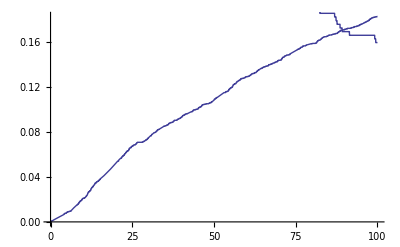

```mathematica
Show[err1,err2]
```

```mathematica
For[k=0.1,k<500,k=k+1,
If[Abs[Length[Select[ddiff,#≥(k)&]]/Length[ddiff]-
Length[Select[dsame,#≤(k)&]]/Length[dsame]]<0.05,Print[k];Break[];]
]
N[Length[Select[dsame,#≤(k)&]]/Length[dsame]]
N[Length[Select[ddiff2,#≥(k)&]]/Length[ddiff2]]
N[Length[Select[dsame2,#≤(k)&]]/Length[dsame2]]
```

9.1

0.814332

0.733726

0.882641

```mathematica
thd+k
```

20.35

```mathematica
(*try Parzen*)
```